```mathematica
ϕ::usage = "potencjał";
```

```mathematica
Laplacian[ϕ[x , y] , {x , y}]
```

ϕ^(0,2)[x,y]+ϕ^(2,0)[x,y]

```mathematica
%//FullForm
```

Plus[Derivative[0,2][\[Phi]][x,y],Derivative[2,0][\[Phi]][x,y]]

```mathematica
Laplacian[ϕ[x , y] , {x , y}] == 0
```

ϕ^(0,2)[x,y]+ϕ^(2,0)[x,y]==0

```mathematica
D[ϕ[x , y] , {x , 2}] + D[ϕ[x , y] , {y , 2}] == 0
```

ϕ^(0,2)[x,y]+ϕ^(2,0)[x,y]==0

```mathematica
(*W zadaniu C:*)
```

```mathematica
(*NSolve -> DSolve*)
```

```mathematica
(*równania -> {D[u[x , y] , x]==... , u[x , 0] == Sin[x] , v[x , 0] == 0}*)
```

```mathematica
(*ϕ -> {u , v}*)
```

```mathematica
(*{x , 0 , 1} , {y , 0 , 1} -> {x , y}*)
```

```mathematica
solution = NDSolve[
{
D[ϕ[x , y] , {x , 2}]+D[ϕ[x , y] , {y , 2}] == 0 , 
ϕ[x , 0] == 0 , 
ϕ[x , 1] == 1 , 
ϕ[0 , y] == y , 
ϕ[1 , y] == y
} , 
ϕ , 
{x , 0 , 1} , {y , 0 , 1}]
```

{{ϕ→InterpolatingFunction[…]}}

```mathematica
ϕ/.solution[[1]]
```

InterpolatingFunction[…]

```mathematica
potentialSolution = ϕ/.solution[[1]];
```

```mathematica
potentialSolution[0.5 , 0.5]
```

0.5

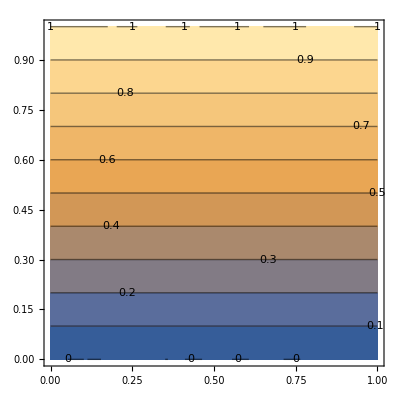

```mathematica
ContourPlot[potentialSolution[x , y] , {x , 0 , 1} , {y , 0 , 1} , ContourLabels->True]
```

```mathematica
a = {{1 , 3} , {2 , 18}};
```

```mathematica
b = {{123 , -1} , {1 , 8}};
```

```mathematica
c = 2 a + π b;
```

```mathematica
c//MatrixForm
```

(2+123 π | 6-π
4+π | 36+8 π)

```mathematica
sol = Solve[c== α a + β b , {α , β}]
```

{{α→2,β→π}}

```mathematica
(α a + β b)/.sol[[1]]//MatrixForm
```

(2+123 π | 6-π
4+π | 36+8 π)

```mathematica
MatrixExp[c]//N//MatrixForm
```

(5.17465×10^168 | 4.51854×10^166
1.12894×10^167 | 9.85796×10^164)

```mathematica
(*f[x]*)
```

```mathematica
(*x//f*)
```

```mathematica
(*g[x , y]*)
```

```mathematica
(*x~g~y*)
```

```mathematica
(*Typ danych dla liczb zespolonych:*)
```

```mathematica
cn::usage = "Liczba zespolona!";
```

```mathematica
real::usage = "Liczba rzeczywista!";
```

```mathematica
real = _Real|_Integer;
```

```mathematica
pair::usage = "Para liczb reprezentujących część rzeczywistą oraz urojoną liczby zespolonej.";
```

```mathematica
cn = real | pair[real , real];
```

```mathematica
MatchQ[123 , cn]
```

True

```mathematica
(**)
```

```mathematica
conjugate::usage = "";
```

```mathematica
conjugate[x:real]:= x;
conjugate[pair[a:real , b:real]]:= pair[a , -b];
```

```mathematica
conjugate[12.3]
```

12.3

```mathematica
conjugate[pair[1 , 2]]
```

pair[1,-2]

```mathematica
(**)
```

```mathematica
plus::usage = "";
```

```mathematica
plus[a:real , b:real]:=pair[a+b , 0];
```

```mathematica
plus[a:real , pair[x:real , y:real]]:=pair[x + a , y];
```

```mathematica
plus[pair[x:real , y:real] , a:real]:= plus[a , pair[x , y]];
```

```mathematica
plus[pair[x:real , y:real] , pair[x1:real , y1:real]]:= pair[x + x1 , y + y1];
```

```mathematica
12.3123//Head
```

Real

```mathematica
1231//Head
```

Integer

```mathematica
(**)
```

```mathematica
times::usage = "";
```

```mathematica
times[a:real , b:real]:=pair[a b   , 0];
```

```mathematica
times[a:real , pair[x:real , y:real]]:=pair[a x   , a y];
```

```mathematica
times[pair[x:real , y:real] , a:real]:= times[a , pair[x , y]];
```

```mathematica
times[pair[x:real , y:real] , pair[x1:real , y1:real]]:= pair[x x1 - y y1 , x y1 + y x1];
```

```mathematica
(**)
```

```mathematica
re::usage = "";
```

```mathematica
re[a:real]:=a;
re[pair[x:real , y:real]]:=x;
```

```mathematica
im::usage = "";
```

```mathematica
im[a:real]:=0;
im[pair[x:real , y:real]]:=y;
```

```mathematica
(**)
```

```mathematica
mul = CurryApplied[times , 2];
```

```mathematica
mulByI = mul[pair[0 , 1]];
```

```mathematica
mulByI[1]
```

pair[0,1]

```mathematica
mulByI[pair[0 , 1]]
```

pair[-1,0]

```mathematica
Nest[f , x , 10]
```

f[f[f[f[f[f[f[f[f[f[x]]]]]]]]]]

```mathematica
power::usage = "";
```

```mathematica
power[n_Integer , z_]:=Nest[mmm[z] , 1 , n];
```

```mathematica
power[2 , x]
```

mmm[x][mmm[x][1]]

```mathematica
power[n_Integer , z_]:=Nest[mul[z] , 1 , n];
```

```mathematica
power[0 , pair[0 , 1]]
```

1

```mathematica
power[1 , pair[0 , 1]]
```

pair[0,1]

```mathematica
power[2 , pair[0 , 1]]
```

pair[-1,0]

```mathematica
Sum[expr[n] , {n , 0 , 100}]//N
```

expr[0]+expr[1]+expr[2]+expr[3]+expr[4]+expr[5]+expr[6]+expr[7]+expr[8]+expr[9]+expr[10]